```mathematica
(*data: the muon decay time data that has already filtered out fake alarms;
  numBin: the number of bins that you want to set up to prepare the muon decay distribution;*)
```

```mathematica
getDist[data_,numBin_]:=Module[
(*maxTime: the largest muon lifetime recorded;
  dist: a list that contains elements of {start_time, count};*)
{minTime,maxTime,t,i,binWidth,dataLen,dist,count},
(* specify the width of each bin. It should not matter that we set the width of each bin to be
slightly larger, i.e. to be the next integer. In this case, the total number of bins to cover
all the data should still be the same. *)
minTime=Min[data];
maxTime=Max[data];
(*Need to have maxTime+1 because the start time of the first bin is 0.*)
binWidth=Ceiling[(maxTime-minTime+1)/numBin];

(* Now we want to create our distribution list of the decay data in form of {start time of decay, number of decays in this bin} *)
dist={};
For[i=0,i≤(numBin-1),i++,
(*So basically each bin is an interval of [start_time, start_time + binWidth)*) 
t=minTime+i*binWidth;
count=Count[data,u_/;u≥t&&u<(t+binWidth)];
AppendTo[dist,{t,count}]
];
{dist, numBin, binWidth}
]
```

```mathematica
(*This is almost the same function as above, except that we can choose the starting time delimter and the
ending time delimiter. Therefore it can somehow be more flexible.
Return: {distList, binWdith, numBin}*)
```

```mathematica
getDist[data_,startTime_, endTime_,numBin_]:=Module[
{binWidth,hisDat,delimits,counts,trueEndTime,trueStartTime, distList,i,lenCounts},

binWidth=Ceiling[(endTime-startTime+1)/numBin];

(*Now I want to determine the true suitable endTime given the bin width.
Therefore, we will always guarantee to have the number of bins as initially intended.
Therefore, this function should always function exactly the same as the previous one,
when startTime was set to be Min[data].*)
trueStartTime=startTime;
If[Mod[endTime - startTime,binWidth]==0,
trueEndTime=endTime,
trueEndTime=startTime+binWidth*numBin];

hisDat= HistogramList[data,{trueStartTime,trueEndTime,binWidth}];
delimits=hisDat[[1]];
counts=hisDat[[2]];
lenCounts=Length[counts];
(*Print[lenCounts];*)

(*Now we want to settle delimits and counts into a distribution list of element {startTime, numCounts}*)
distList={};
(*Print["Hey"];
Print[i];
Print[Length[counts]];*)
For[i=1,i≤lenCounts,i++,
(*Print[i];*)
AppendTo[distList,{delimits[[i]],counts[[i]]}];
(*Print[i,": ",distList];*)
];
{distList, binWidth,numBin}
]
```

```mathematica
(*data: the muon decay time data that has already filtered out fake alarms
numBin: the number of bins that we want to partitionthresh
thresh: the threshhold of the decay time that we want to keep*)
```

```mathematica
getLogList[data_,numBin_,thresh_]:=Module[
{dataThresh,dataDist,dataDistLog},
(*Subtracting the very first data points with small decay times.*)
dataThresh=Select[data,#>thresh&];

dataDist=getDist[dataThresh,numBin][[1]];
dataDistLog={#[[1]],Log@#[[2]]}&/@dataDist;
dataDistLog
]
```

```mathematica
(*@Return {cleanedDat, its length, its min time, its max time}: a cleaned, sorted data list of elements of time*)
cleanRawData[rawData_]:=Module[
{dat},
dat=Select[rawData,#[[1]]<40000&];
dat=#[[1]]&/@dat;
dat=Sort[dat];
{dat, Length[dat],Min[dat],Max[dat]}
];
```

```mathematica
(*All the code above are pre-defined functions.*)
```

```mathematica
m3d=Import["/Users/benxgh1996/Desktop/Muon/muon_3.data","Table"]
```

{{40000,1520372689},{40000,1520372690},{40013,1520372691},{40003,1520372692},{40005,1520372693},{40006,1520372694},{40006,1520372695},{40008,1520372696},{40008,1520372697},{40008,1520372698},{40008,1520372699},{40005,1520372700},{40005,1520372701},{40003,1520372702},602961,{40000,1520968214},{40001,1520968215},{40002,1520968216},{40001,1520968217},{40001,1520968218},{40,1520968218},{40004,1520968219},{40001,1520968220},{40001,1520968221},{40000,1520968222},{40000,1520968223},{40000,1520968224},{40000,1520968225},{40000,1520968226}}
 |  |  |  |

```mathematica
{m3dtSort,m3Len,min3,max3}=cleanRawData[m3d];
```

```mathematica
{m3Len,min3,max3}
```

{8852,40,19880}

```mathematica
{m1dtSort,m1Len,min1,max1}=cleanRawData[m1df];
```

```mathematica
{m2dtSort,m2Len,min2,max2}=cleanRawData[m2d];
```

```mathematica
{m1Len,m2Len}
```

{2769,1299}

```mathematica
mtDat=Join[m1dtSort,m2dtSort,m3dtSort]
```

{40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,12800,11540,11540,11560,11600,11700,11800,11800,11840,11860,11880,11940,11960,11980,12080,12080,12160,12200,12240,12240,12380,12420,12520,12540,12600,12800,13500,13540,13800,14240,14260,14520,15060,15220,15260,15320,16060,16400,16520,16620,16780,16840,17120,17160,17460,17800,17880,18520,18860,18880,19000,19040,19060,19220,19260,19320,19440,19440,19700,19780,19880}
 |  |  |  |

```mathematica
Length[mtDat]
```

12920

```mathematica
mDat=Sort[mtDat]
```

{40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,12800,14260,14260,14520,14660,14780,14880,15060,15140,15140,15160,15160,15220,15260,15320,15480,15620,15640,16060,16400,16520,16620,16740,16780,16840,16940,16940,17020,17120,17160,17280,17460,17520,17580,17680,17800,17880,18520,18580,18600,18600,18860,18860,18880,18880,19000,19040,19060,19180,19200,19220,19240,19260,19320,19440,19440,19500,19700,19780,19820,19880}
 |  |  |  |

```mathematica
Export["muon_dat.xlsx",mDat,"Data"]
```

muon_dat.xlsx

```mathematica
Export["muon_dat_1.xlsx",m1dtSort,"Data"]
```

muon_dat_1.xlsx

```mathematica
Export["muon_dat_2.xlsx",m2dtSort,"Data"]
```

muon_dat_2.xlsx

```mathematica
Export["muon_dat_3.xlsx",m3dtSort,"Data"]
```

muon_dat_3.xlsx

```mathematica
{m3dist,m3BinWidth,m3NumBin}=getDist[m3dtSort,Min[m3dtSort], Max[m3dtSort],300]
```

{{{m3dtSort⟦1⟧,m3dtSort},{m3dtSort⟦2⟧,m3dtSort},{m3dtSort⟦3⟧,1}},1,300}

```mathematica
getDist[m3dtSort,Min[m3dtSort], Max[m3dtSort],300]
```

getDist[m3dtSort,m3dtSort,m3dtSort,300]

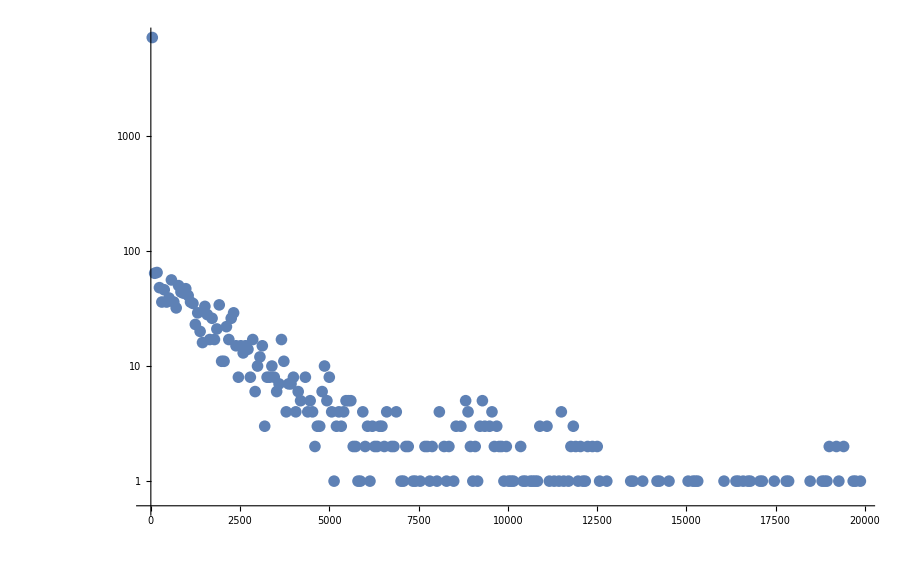

```mathematica
ListPlot[m3dist,ScalingFunctions->"Log"]
```

```mathematica
m1d=Import["/Users/benxgh1996/Desktop/Muon/muon_1.data","Table"]
```

{{40000,1518120833},{40000,1518120834},{40005,1518120835},{40003,1518120836},{40003,1518120837},{40000,1518120838},{40004,1518120839},{40002,1518120840},{40002,1518120841},{40003,1518120842},{40006,1518120843},{40009,1518120844},{40002,1518120845},{40000,1518120846},791076,{40006,1519934343},{40008,1519934344},{40004,1519934345},{40005,1519934346},{40005,1519934347},{40003,1519934348},{40005,1519934349},{40006,1519934350},{40004,1519934351},{40004,1519934352},{40007,1519934353},{40005,1519934354},{40006,1519934355},{40000,1519934356}}
 |  |  |  |

```mathematica
(*Filtered data that only contains measurements of our first lab day *)
```

```mathematica
m1df=Select[m1d,#[[2]]>=1519770660&&#[[1]]<40000&]
```

{{40,1519770662},{100,1519770710},{40,1519770761},{40,1519770907},{40,1519770971},{40,1519771041},{540,1519771091},{40,1519771098},{40,1519771140},{2580,1519771157},{40,1519771218},{40,1519771225},{40,1519771266},{40,1519771303},{5160,1519771509},{40,1519771515},2737,{11320,1519933792},{40,1519933824},{40,1519933824},{40,1519933827},{40,1519933876},{3460,1519933981},{40,1519934000},{40,1519934075},{40,1519934077},{820,1519934095},{40,1519934124},{40,1519934167},{5200,1519934187},{40,1519934195},{40,1519934262},{4460,1519934333}}
 |  |  |  |

```mathematica
m1dt=#[[1]]&/@m1df
```

```mathematica
m1dtSort=Sort[m1dt]
```

```mathematica
Count[m1dt,u_/;u>60]
```

697

```mathematica
Length[m1dtSort]
```

2769

```mathematica
m1dtLarge=Select[m1dtSort, #>100&]
```

```mathematica
m1Log300=getLogList[m1dtLarge,20,300]
```

{{320,Log[205]},{1235,Log[131]},{2150,Log[76]},{3065,Log[46]},{3980,Log[39]},{4895,Log[30]},{5810,Log[15]},{6725,Log[6]},{7640,Log[10]},{8555,Log[10]},{9470,Log[5]},{10385,Log[3]},{11300,Log[5]},{12215,Log[2]},{13130,0},{14045,Log[5]},{14960,Log[5]},{15875,0},{16790,Log[3]},{17705,0}}

```mathematica
Select[m1Log300,]
```

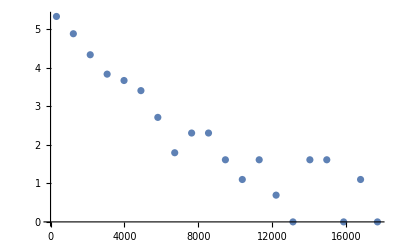

```mathematica
ListPlot[Tooltip[m1Log300],#[[1]]<=12215&]
```

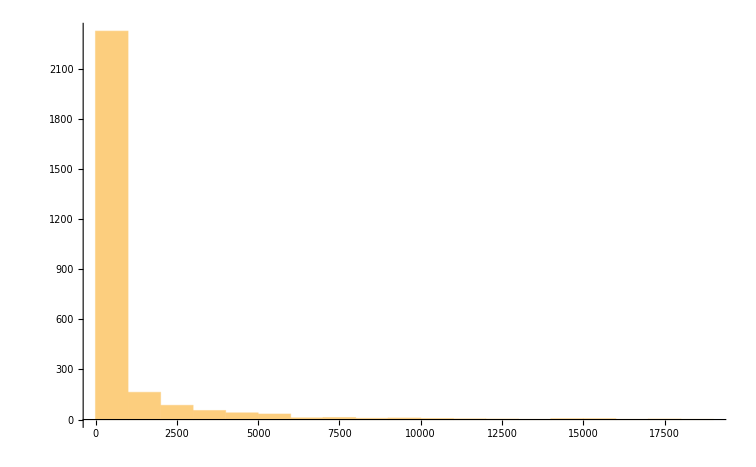

```mathematica
Histogram[m1dt,20]
```

```mathematica
Max[m1dtSort]
```

18600

```mathematica
Length[m1dtSort]
```

2769

```mathematica
getDist[m1dtSort,20]
```

{{{40,2322},{969,156},{1898,80},{2827,58},{3756,47},{4685,30},{5614,17},{6543,6},{7472,11},{8401,9},{9330,6},{10259,4},{11188,4},{12117,3},{13046,1},{13975,5},{14904,5},{15833,1},{16762,3},{17691,1}},20,929}

```mathematica
#[[2]]&/@%109[[1]]
```

{2322,156,80,58,47,30,17,6,11,9,6,4,4,3,1,5,5,1,3,1}

```mathematica
Total[%111]
```

2769

```mathematica
list=Select[m1dtSort,#>300&]
```

```mathematica
Min[list]
```

320

```mathematica
getDist[list,20][[1]]
```

{}

```mathematica
getLogList[m1dtSort,20,300]
```

{}

```mathematica
getDist[m1dtSort,20][[1]]
```

{{0,2312},{931,164},{1862,76},{2793,63},{3724,48},{4655,30},{5586,17},{6517,6},{7448,11},{8379,8},{9310,7},{10241,4},{11172,4},{12103,3},{13034,1},{13965,5},{14896,5},{15827,1},{16758,3},{17689,1}}

```mathematica
(*This is the histogram distribution of data m1*)
```

```mathematica
m1Dist=getDist[m1dtSort,20][[1]]
```

{{0,2312},{931,164},{1862,76},{2793,63},{3724,48},{4655,30},{5586,17},{6517,6},{7448,11},{8379,8},{9310,7},{10241,4},{11172,4},{12103,3},{13034,1},{13965,5},{14896,5},{15827,1},{16758,3},{17689,1}}

```mathematica
#[[2]]&/@m1Dist
```

```mathematica
Total[{2312,164,76,63,48,30,17,6,11,8,7,4,4,3,1,5,5,1,3,1}]
```

2769

```mathematica
m1LogDist={#[[1]],Log@#[[2]]}&/@m1Dist
```

{{0,Log[2312]},{931,Log[164]},{1862,Log[76]},{2793,Log[63]},{3724,Log[48]},{4655,Log[30]},{5586,Log[17]},{6517,Log[6]},{7448,Log[11]},{8379,Log[8]},{9310,Log[7]},{10241,Log[4]},{11172,Log[4]},{12103,Log[3]},{13034,0},{13965,Log[5]},{14896,Log[5]},{15827,0},{16758,Log[3]},{17689,0}}

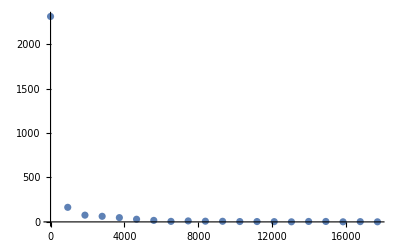

```mathematica
ListPlot[m1Dist,PlotRange->All]
```

```mathematica
nf=Nearest[m1LogDist];
```

```mathematica
ListPlot[m1LogDist,
Epilog->Dynamic@DynamicModule[{pt=nf[MousePosition[{"Graphics",Graphics},{0,0}]],scaled=MousePosition[{"GraphicsScaled",Graphics},None]},If[scaled===None,{},{Text[pt[[1]],pt[[1]],{1.5 Sign[scaled[[1]]-.5],0},Background-> White],AbsolutePointSize[7],Point[pt],Black,AbsolutePointSize[5],Point[pt]}]]]
```

-Graphics-

```mathematica
FindFit[m1LogDist,-λ x +b,{λ,b},x]
```

{λ→0.000311671,b→5.14802}

```mathematica
1/λ/.λ->0.0003116706209601906
```

3208.52

```mathematica
(*m1LogClear is m1LogDist that excludes data in the first channel and in the last channels*)
```

```mathematica
m1LogClear=Select[m1LogDist,(#[[1]]>931&&#[[1]]<13034)&]
```

{{1862,Log[76]},{2793,Log[63]},{3724,Log[48]},{4655,Log[30]},{5586,Log[17]},{6517,Log[6]},{7448,Log[11]},{8379,Log[8]},{9310,Log[7]},{10241,Log[4]},{11172,Log[4]},{12103,Log[3]}}

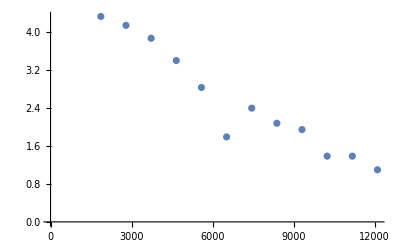

```mathematica
ListPlot[Tooltip[m1LogClear]]
```

```mathematica
FindFit[m1LogClear,-λ t+b,{λ,b},t]
```

{λ→0.00032558,b→4.82884}

```mathematica
1/λ/.λ->0.0003255798981858529
```

3071.44

```mathematica
m2d=Import["/Users/benxgh1996/Desktop/Muon/muon_2.data","Table"]
```

{{40000,1519943777},{40000,1519943778},{40003,1519943779},{40000,1519943780},{40001,1519943781},{40001,1519943782},{40000,1519943783},{40000,1519943784},{40000,1519943785},{40001,1519943786},{40001,1519943787},{40001,1519943788},{40000,1519943789},{40000,1519943790},422730,{40000,1520366317},{40000,1520366318},{40000,1520366319},{40000,1520366320},{40000,1520366321},{40000,1520366322},{40000,1520366323},{40000,1520366324},{40002,1520366325},{40003,1520366326},{40000,1520366327},{40000,1520366328},{40000,1520366329},{40000,1520366330}}
 |  |  |  |

```mathematica
m2df=Select[m2d,#[[1]]<40000&]
```

```mathematica
m2dt=#[[1]]&/@m2df
```

```mathematica
m2dtSort=Sort[m2dt]
```

```mathematica
Length[m2dt]
```

1299

```mathematica
m3d=Import["/Users/benxgh1996/Desktop/Muon/muon_3.data","Table"]
```

{{40000,1520372689},{40000,1520372690},{40013,1520372691},{40003,1520372692},{40005,1520372693},{40006,1520372694},{40006,1520372695},{40008,1520372696},{40008,1520372697},{40008,1520372698},{40008,1520372699},{40005,1520372700},{40005,1520372701},{40003,1520372702},602961,{40000,1520968214},{40001,1520968215},{40002,1520968216},{40001,1520968217},{40001,1520968218},{40,1520968218},{40004,1520968219},{40001,1520968220},{40001,1520968221},{40000,1520968222},{40000,1520968223},{40000,1520968224},{40000,1520968225},{40000,1520968226}}
 |  |  |  |

```mathematica
m3df=Select[m3d,#[[1]]<40000&]；
```

{{1080 ；,1520372848 ；},{100 ；,1520373057 ；},{80 ；,1520373057 ；},{80 ；,1520373057 ；},{360 ；,1520373057 ；},{100 ；,1520373057 ；},{540 ；,1520373057 ；},{40 ；,1520373106 ；},{40 ；,1520373129 ；},{40 ；,1520373242 ；},{40 ；,1520373666 ；},{120 ；,1520373766 ；},{60 ；,1520373857 ；},8827,{140 ；,1520967740 ；},{40 ；,1520967745 ；},{100 ；,1520967752 ；},{40 ；,1520967818 ；},{40 ；,1520967906 ；},{40 ；,1520967982 ；},{60 ；,1520967988 ；},{40 ；,1520968029 ；},{1020 ；,1520968033 ；},{40 ；,1520968034 ；},{40 ；,1520968159 ；},{40 ；,1520968218 ；}}
 |  |  |  |

```mathematica
m3dt=#[[1]]&/@m3df;
```

```mathematica
m3dtSort=Sort[m3dt]；
```

{40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,40 ；,8770,12380 ；,12420 ；,12520 ；,12540 ；,12600 ；,12800 ；,13500 ；,13540 ；,13800 ；,14240 ；,14260 ；,14520 ；,15060 ；,15220 ；,15260 ；,15320 ；,16060 ；,16400 ；,16520 ；,16620 ；,16780 ；,16840 ；,17120 ；,17160 ；,17460 ；,17800 ；,17880 ；,18520 ；,18860 ；,18880 ；,19000 ；,19040 ；,19060 ；,19220 ；,19260 ；,19320 ；,19440 ；,19440 ；,19700 ；,19780 ；,19880 ；}
 |  |  |  |

```mathematica
Length[m3dtSort]
```

8852

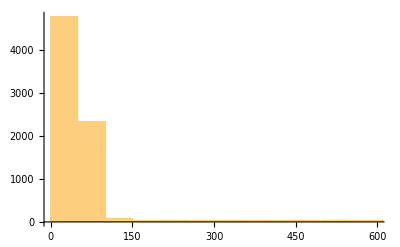

```mathematica
Histogram[m3dtSort,300]
```

```mathematica
Max[m3dtSort]
```

19880

```mathematica
Count[m3dtSort,u_/;u≥300]
```

1534

```mathematica
HistogramList[m3dtSort,{300,20100,200}]
```

{{300,500,700,900,1100,1300,1500,1700,1900,2100,2300,2500,2700,2900,3100,3300,3500,3700,3900,4100,4300,4500,4700,4900,5100,5300,5500,5700,5900,6100,6300,6500,6700,6900,7100,7300,7500,7700,7900,8100,8300,8500,8700,8900,9100,9300,9500,9700,9900,10100,10300,10500,10700,10900,11100,11300,11500,11700,11900,12100,12300,12500,12700,12900,13100,13300,13500,13700,13900,14100,14300,14500,14700,14900,15100,15300,15500,15700,15900,16100,16300,16500,16700,16900,17100,17300,17500,17700,17900,18100,18300,18500,18700,18900,19100,19300,19500,19700,19900,20100},{122,134,120,137,96,62,80,69,55,61,59,41,32,34,28,21,32,24,19,14,15,9,16,19,7,15,12,4,7,7,10,6,5,5,4,2,2,4,3,6,3,4,8,7,6,8,9,7,4,2,3,2,3,3,4,2,5,6,5,4,2,3,1,0,0,0,2,1,0,2,0,1,0,1,2,1,0,0,1,0,1,2,2,0,2,1,0,2,0,0,0,1,2,3,2,3,0,3,0}}

```mathematica
Length[HistogramList[m3dtSort,{300,20100,200}][[1]]]
```

100

```mathematica
Length[HistogramList[m3dtSort,{300,20100,200}][[2]]]
```

99

```mathematica
Total[HistogramList[m3dtSort,{300,19890,200}][[2]]]
```

1531

```mathematica
Count[m2dt,u_/;u≤60]
```

460

```mathematica
expo[τ_,x_]:=1/τ*ⅇ^(-x/τ)
```

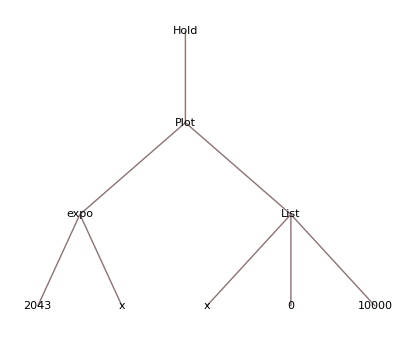

```mathematica
TreeForm@Hold[Plot[expo[2043,x],{x,0,10000}]]
```

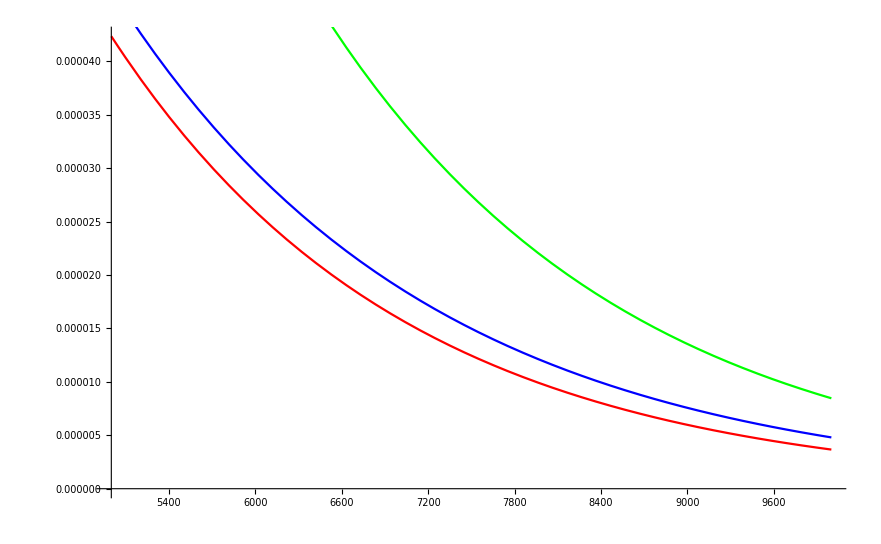

```mathematica
Show[Plot[expo[2043,x],{x,5000,10000},PlotStyle->Red],Plot[expo[2197,x],{x,5000,10000},PlotStyle->Blue],Plot[expo[2043,x]+expo[2197,x],{x,5000,10000},PlotStyle->Green]]
```

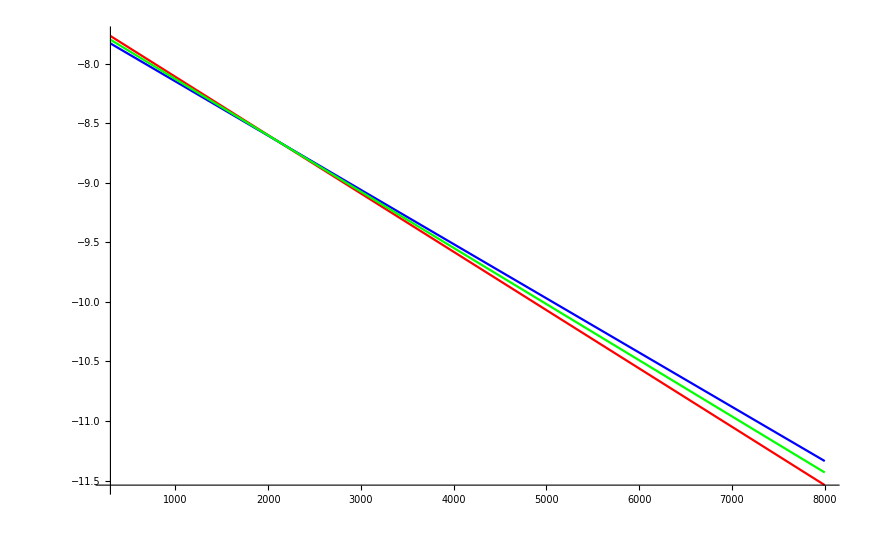

```mathematica
{startTime,endTime}={300,8000};
Show[Plot[Log[expo[2043,x]],{x,startTime,endTime},PlotStyle->Red],Plot[Log[expo[2197,x]],{x,startTime,endTime},PlotStyle->Blue],Plot[Log[1/2]+Log[expo[2043,x]+expo[2197,x]],{x,startTime,endTime},PlotStyle->Green],PlotRange-> All]
```

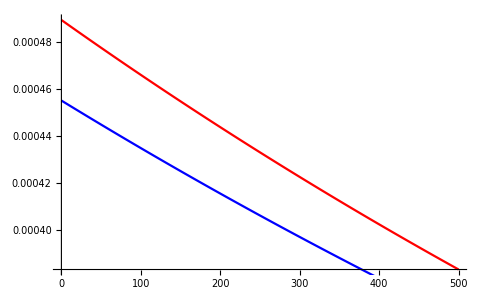

```mathematica
Show[Plot[expo[2043,x],{x,0,500},PlotStyle->Red],Plot[expo[2197,x],{x,0,500},PlotStyle->Blue]]
```